# Creating Movies and Animations in Mathematica

Christopher Lum
lum@uw.edu

This document accompanies the YouTube video at https://youtu.be/S03e6dwM100.

## Simple Animations

Consider a simple function

	f(t)=A sin(ω t)

```mathematica
f[t_,A_,ω_]=A Sin[ω t];
```

Make a simple static plot

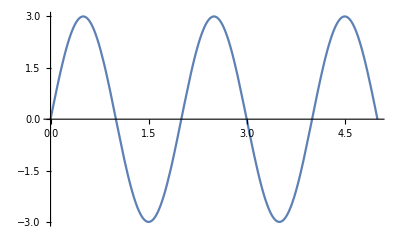

```mathematica
AExample=3;
ωExample=π;

Plot[f[t,AExample,ωExample],{t,0,5}]
```

Mathematica provides the ‘Manipulate’ function to generate an expression with an interactive window to change one or more parameters.

```mathematica
Manipulate[m*x+3,{m,2,4}]
```

We can combine ‘Manipulate’ with plotting commands to generate animations.

```mathematica
Manipulate[
Plot[f[t,A,ω],{t,0,5}],
{ω,1,5}
]
```

You can even change more than 1 parameter at a time.

```mathematica
Manipulate[
Plot[f[t,A,ω],{t,0,5}],
{ω,1,5},
{A,2,4}
]
```

## Animation Theory

See ‘Creating Movies and Animations in Matlab’ video (first 10 minutes) located at https://youtu.be/3I1_ 5M7Okqo.

## Animations in Mathematica

Recall that example trajectory/parameterization is

	r̄(t)=(x(t)
y(t)
z(t))=(5 cos(t)
2 sin(t)
t)
	
	for t∈[0, 2 π]

### Step 1: Generate Data

Define the aforementioned parameterization

```mathematica
x[t_]=5 Cos[t];
y[t_]=2 Sin[t];
z[t_]=t;

(*Check that this looks reasonable with a static plot*)
ParametricPlot3D[{x[t],y[t],z[t]},{t,0,2 π}]
```

-Graphics3D-

Setup a range of times where we would like to animate or render the scenario (t∈[0, 2π]).

```mathematica
tRange=Range[0, 2 π,(2 π)/99];   (*Create 100 time steps, saved as a list*)
```

Define/initialize a container that will be used to hold the frames of animation.

```mathematica
movieVector=ConstantArray[0,Length[tRange]];  (*saved as a list*)
```

### Step 2: Draw/Render the Scenario

### Step 3: Take a Snapshot

### Step 4: Advance Time Forward

Use a ‘for’ loop to create frames of animation

```mathematica
For[k=1,k≤Length[tRange],k++,
(*Extract data for a single point*)
tk=tRange[[k]];
xk=x[tk];
yk=y[tk];
zk=z[tk];

(*Render the scenario*)
movieVector[[k]]=Show[
(*Plotting just the point as a green dot*)
Graphics3D[
{
AbsolutePointSize[15],Green, Point[{xk,yk,zk}]
}
],

(*draw the entire trajectory/curve*)
ParametricPlot3D[{x[t],y[t],z[t]},{t,0,2 π}],

(*Decorate the plot*)
AxesLabel->{"x","y","z"},
PlotLabel->StringJoin["t = ", ToString[N[tk]]]
]
]
```

### Step 5: Save Movie

Now export the movieVector object as a single .avi file

```mathematica
fileName="curveMathematica.avi";
Export[fileName,movieVector];
```

You can find where Mathematica stores the file using the ‘Directory’ command

```mathematica
Directory[]
```

C:\Users\chris\Documents